```mathematica
Clear["Global`*"]
```

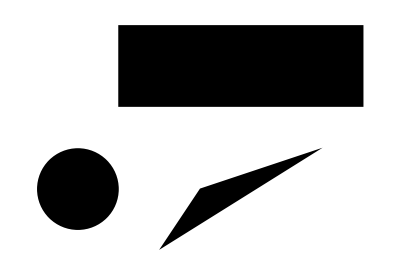

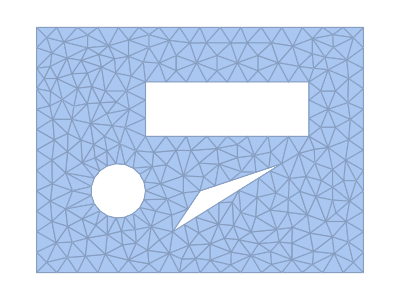

502

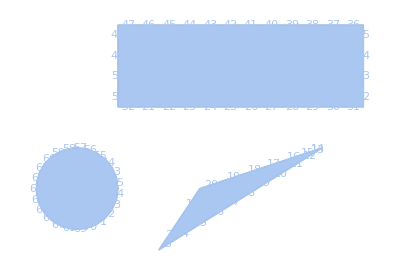

75

```mathematica
Geometry={Disk[],Rectangle[{1,2},{7,4}],Triangle[{{3,0},{6,1},{2,-1.5}}]};

Graphics[Geometry]

DiscretizeRegion[RegionDifference[Rectangle[{-3,-3},{9,6}],RegionUnion@@Geometry]]
MeshCellCount[%,2]

ϵ0=8.85418782*10^-12;

HighlightMesh[bMesh=BoundaryMesh[DiscretizeRegion[RegionUnion@@Geometry]],Labeled[1,"Index"]]
NEl=MeshCellCount[%,1]
```

```mathematica
GreenF[x_,x0_]:=-N[1/2/Pi Log[Norm[x-x0]]]
DGreenF[x_,x0_]:=-N[1/2/Pi/Norm[x-x0]]

BElts=MeshPrimitives[bMesh,1];
Knots=RegionCentroid/@BElts;

G=ParallelTable[If[i!=j,RegionMeasure[BElts[[j]]]*NIntegrate[GreenF[Knots[[i]],BElts[[j,1,1]]+t(BElts[[j,1,2]]-BElts[[j,1,1]])],{t,0,1},Method->{Automatic,"SymbolicProcessing"->0}],0],{i,1,NEl},{j,1,NEl}];
G=G+DiagonalMatrix[ParallelTable[#/Pi (1-Log[#])&[RegionMeasure[BElts[[i]]]/2] ,{i,1,NEl}]];
```

```mathematica
H=Transpose[(RegionMeasure/@BElts )Transpose[ParallelTable[If[i!=j,NIntegrate[({-#[[2]],#[[1]]}/Norm[#]&[(BElts[[j,1,2]]-BElts[[j,1,1]])]).(#/Norm[#]&[BElts[[j,1,1]]+t(BElts[[j,1,2]]-BElts[[j,1,1]])-Knots[[i]]])DGreenF[Knots[[i]],BElts[[j,1,1]]+t(BElts[[j,1,2]]-BElts[[j,1,1]])],{t,0,1},AccuracyGoal->15,Method->{Automatic,"SymbolicProcessing"->0}],0],{i,1,NEl},{j,1,NEl}]]];
H=H+1/2IdentityMatrix[NEl];
```

9.611×10^-11

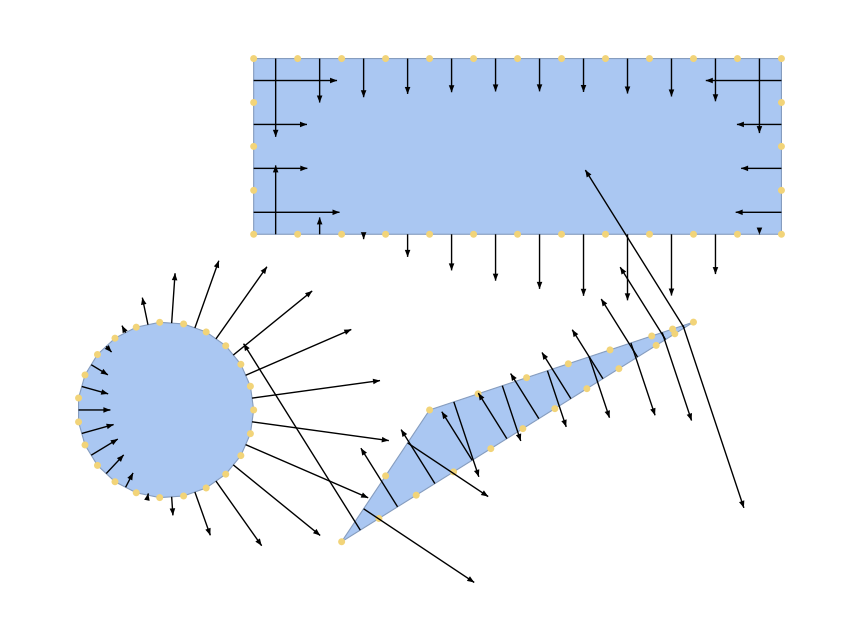

```mathematica
u0D=ConstantArray[1.,Length[MeshCells[bMesh,2][[1,1]]]]~Join~ConstantArray[2.,Length[MeshCells[bMesh,2][[2,1]]]]~Join~ConstantArray[3.,Length[MeshCells[bMesh,2][[3,1]]]];
qSol=LinearSolve[G,H.u0D];

qTot=-Sum[RegionMeasure[BElts[[j]]]*qSol[[j]],{j,1,NEl}]*ϵ0

Show[HighlightMesh[bMesh,0],Graphics[{Arrowheads[.02],Table[Arrow[{Knots[[i]],Knots[[i]]-(qSol[[i]]{-#[[2]],#[[1]]}/Norm[#]&[(BElts[[i,1,2]]-BElts[[i,1,1]])])}],{i,1,NEl}]}]]
```

```mathematica
(*Убеждаемся, что граничные элементы направлены в одну сторону на контуре*)
MeshCellCount[bMesh,1](*считаем сколько отрезков содержит граница с возможными общими началами или концами отрезков*)
Length[DeleteDuplicatesBy[MeshCells[bMesh,1],#[[1,1]]&]](*считаем сколько отрезков содержит граница без возможности общего начала*)
Length[DeleteDuplicatesBy[MeshCells[bMesh,1],#[[1,2]]&]](*считаем сколько отрезков содержит граница без возможности общего конца*)
```

75

75

75

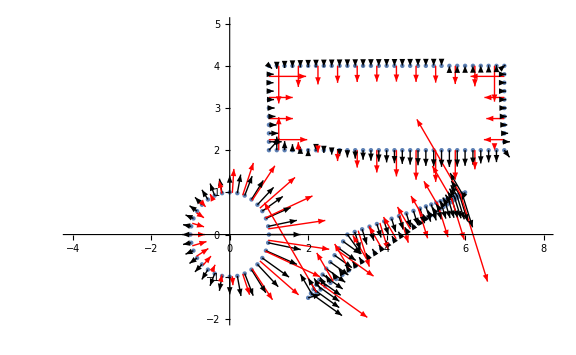

```mathematica
(*сравниваем решение семинарской задачи на границе и решение в COMSOL*)
data=Import[NotebookDirectory[]<>"/dz11comsol/E.csv"][[9;;]];
Length[data];
KnotsComsol=Transpose[{data[[All,1]],data[[All,2]]}];
eVect=Transpose[{data[[All,3]],data[[All,4]]}];
Show[ListPlot[KnotsComsol,ImageSize->Large,PlotRange->{{-4,8},{-2,5}}],Graphics[{Arrowheads[.02],Table[Arrow[{KnotsComsol[[i]],KnotsComsol[[i]]+eVect[[i]]}],{i,1,Length[KnotsComsol]}]},ImageSize->Large],Graphics[{Red,Arrowheads[.02],Table[Arrow[{Knots[[i]],Knots[[i]]-(qSol[[i]]{-#[[2]],#[[1]]}/Norm[#]&[(BElts[[i,1,2]]-BElts[[i,1,1]])])}],{i,1,NEl}]}]]
```

```mathematica
(*сравниваем решение семинарской задачи и решение в COMSOL вдали от стержней на границе окна разбиения в COMSOL*)
```

```mathematica
v[dot_]:=Quiet@ParallelSum[RegionMeasure[BElts[[j]]]*qSol[[j]]*Quiet@NIntegrate[GreenF[dot,BElts[[j,1,1]]+t(BElts[[j,1,2]]-BElts[[j,1,1]])],{t,0,1},Method->{Automatic,"SymbolicProcessing"->0}],{j,1,NEl}]-Quiet@ParallelSum[RegionMeasure[BElts[[j]]]*u0D[[j]]*Quiet@NIntegrate[(({-#[[2]],#[[1]]}/Norm[#]&[(BElts[[j,1,2]]-BElts[[j,1,1]])]).(#/Norm[#]&[BElts[[j,1,1]]+t(BElts[[j,1,2]]-BElts[[j,1,1]])-dot]))*DGreenF[dot,BElts[[j,1,1]]+t(BElts[[j,1,2]]-BElts[[j,1,1]])],{t,0,1},Method->{Automatic,"SymbolicProcessing"->0}],{j,1,NEl}];
v[{13,0.1}]
dataV=Import[NotebookDirectory[]<>"/dz11comsol/V.csv"][[9;;]];
Select[dataV,Norm[{#[[1]],#[[2]]}-{13,0.1}]<0.01&]
```

3.79953

{{13,0.1,3.97348}}

```mathematica
(*метод граничных элементов по сетке COMSOL*)
```

```mathematica
comsMesh=Import[NotebookDirectory[]<>"/dz11comsol/v2d.csv"][[9;;]][[All,{1,2}]];
res=Flatten/@Transpose[{comsMesh,ParallelMap[v,comsMesh]}];
ListPlot3D[res,ColorFunction->"TemperatureMap",ImageSize->Large]
```

-Graphics3D-

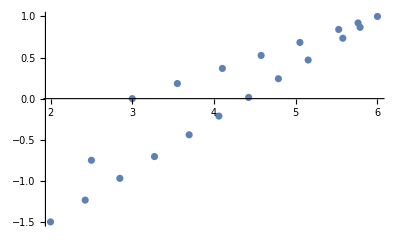

```mathematica
ListPlot[MeshCoordinates[bMesh][[MeshCells[bMesh,2][[1,1]]]]]
```

```mathematica
(*3 Прямоугольник - металл, потенциал 1В; Диск - диэлектрик, поле 2 В/м; Треугольник - металл, полный заряд 1нКл*)
```

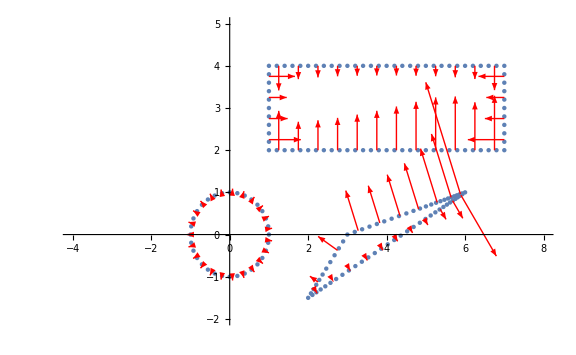

```mathematica
rectphi=1.;
diskE=2.;
fullQ=10^-9;
ϵ0=8.85418782*10^-12;
u0=ConstantArray[u0tr,Length[MeshCells[bMesh,2][[1,1]]]]~Join~ConstantArray[rectphi,Length[MeshCells[bMesh,2][[2,1]]]]~Join~Table[Subscript[u0disk,i],{i,Length[MeshCells[bMesh,2][[3,1]]]}];
q0=Table[Subscript[q0tr,i],{i,Length[MeshCells[bMesh,2][[1,1]]]}]~Join~Table[Subscript[q0rect,i],{i,Length[MeshCells[bMesh,2][[2,1]]]}]~Join~ConstantArray[diskE,Length[MeshCells[bMesh,2][[3,1]]]];
vars=Flatten[{u0tr,Table[Subscript[u0disk,i],{i,Length[MeshCells[bMesh,2][[3,1]]]}],Table[Subscript[q0tr,i],{i,Length[MeshCells[bMesh,2][[1,1]]]}],Table[Subscript[q0rect,i],{i,Length[MeshCells[bMesh,2][[2,1]]]}]}];
eqs={G.q0==H.u0,Total[Table[RegionMeasure[BElts[[i]]]*Subscript[q0tr,i],{i,Length[MeshCells[bMesh,2][[1,1]]]}]]==fullQ/ϵ0};
sol3=Solve[eqs,vars];
qres=Flatten[q0/.sol3];
ures=Flatten[u0/.sol3];
Show[ListPlot[KnotsComsol,ImageSize->Large,PlotRange->{{-4,8},{-2,5}}],Graphics[{Red,Arrowheads[.02],Table[Arrow[{Knots[[i]],Knots[[i]]-0.05(qres[[i]]{-#[[2]],#[[1]]}/Norm[#]&[(BElts[[i,1,2]]-BElts[[i,1,1]])])}],{i,1,NEl}]}]]
```

```mathematica
v2[dot_]:=Total[ParallelTable[RegionMeasure[BElts[[j]]]*qres[[j]]*NIntegrate[GreenF[dot,BElts[[j,1,1]]+t(BElts[[j,1,2]]-BElts[[j,1,1]])],{t,0,1},Method->{Automatic,"SymbolicProcessing"->0}],{j,1,NEl}]]-Total[ParallelTable[RegionMeasure[BElts[[j]]]*ures[[j]]*NIntegrate[(({-#[[2]],#[[1]]}/Norm[#]&[(BElts[[j,1,2]]-BElts[[j,1,1]])]).(#/Norm[#]&[BElts[[j,1,1]]+t(BElts[[j,1,2]]-BElts[[j,1,1]])-dot]))*DGreenF[dot,BElts[[j,1,1]]+t(BElts[[j,1,2]]-BElts[[j,1,1]])],{t,0,1},Method->{Automatic,"SymbolicProcessing"->0}],{j,1,NEl}]];
```

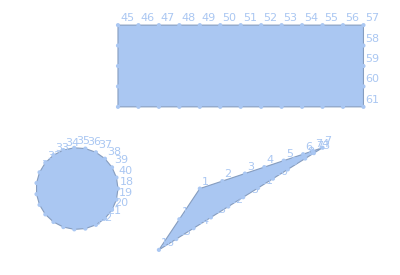

```mathematica
HighlightMesh[bMesh=BoundaryMesh[DiscretizeRegion[RegionUnion@@Geometry]],Labeled[0,"Index"]]
```

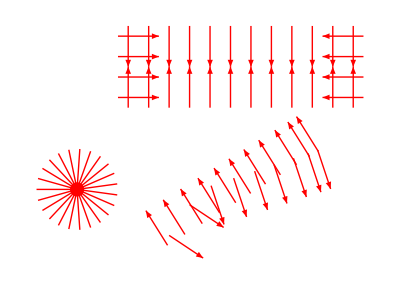

```mathematica
Graphics[{Red,Arrowheads[.02],Table[Arrow[{Knots[[i]],Knots[[i]]+(1*{-#[[2]],#[[1]]}/Norm[#]&[(BElts[[i,1,2]]-BElts[[i,1,1]])])}],{i,1,NEl}]}]
```